```mathematica
<<SPQR`
```

Get::noopen: Cannot open SPQR`.

$Failed

```mathematica
<<spqr_load.m
```

SPℚR: loaded successfully

## Envelope

```mathematica
u = x[1]*x[2]*x[3] + x[1]*x[2]*x[4] + x[1]*x[2]*x[6] + x[1]*x[3]*x[4] + x[1]*x[3]*x[5] + x[1]*x[3]*x[6] + x[1]*x[4]*x[5] + x[1]*x[5]*x[6] + x[2]*x[3]*x[4] + x[2]*x[3]*x[5] + x[2]*x[4]*x[5] + x[2]*x[4]*x[6] + x[2]*x[5]*x[6] + x[3]*x[4]*x[6] + x[3]*x[5]*x[6] + x[4]*x[5]*x[6] // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
f = -m2*x[1]^2*x[2]*x[3] - m2*x[1]^2*x[2]*x[4] - m2*x[1]^2*x[2]*x[6] - m2*x[1]^2*x[3]*x[4] - m2*x[1]^2*x[3]*x[5] - m2*x[1]^2*x[3]*x[6] - m2*x[1]^2*x[4]*x[5] - m2*x[1]^2*x[5]*x[6] - m2*x[1]*x[2]^2*x[3] - m2*x[1]*x[2]^2*x[4] - m2*x[1]*x[2]^2*x[6] - m2*x[1]*x[2]*x[3]^2 + (-4*m2 - s - t)*x[1]*x[2]*x[3]*x[4] - 3*m2*x[1]*x[2]*x[3]*x[5] - 3*m2*x[1]*x[2]*x[3]*x[6] - m2*x[1]*x[2]*x[4]^2 - 3*m2*x[1]*x[2]*x[4]*x[5] - 3*m2*x[1]*x[2]*x[4]*x[6] - 3*m2*x[1]*x[2]*x[5]*x[6] - m2*x[1]*x[2]*x[6]^2 - m2*x[1]*x[3]^2*x[4] - m2*x[1]*x[3]^2*x[5] - m2*x[1]*x[3]^2*x[6] - m2*x[1]*x[3]*x[4]^2 - 3*m2*x[1]*x[3]*x[4]*x[5] - 3*m2*x[1]*x[3]*x[4]*x[6] - m2*x[1]*x[3]*x[5]^2 + (-4*m2 + s)*x[1]*x[3]*x[5]*x[6] - m2*x[1]*x[3]*x[6]^2 - m2*x[1]*x[4]^2*x[5] - m2*x[1]*x[4]*x[5]^2 - 3*m2*x[1]*x[4]*x[5]*x[6] - m2*x[1]*x[5]^2*x[6] - m2*x[1]*x[5]*x[6]^2 - m2*x[2]^2*x[3]*x[4] - m2*x[2]^2*x[3]*x[5] - m2*x[2]^2*x[4]*x[5] - m2*x[2]^2*x[4]*x[6] - m2*x[2]^2*x[5]*x[6] - m2*x[2]*x[3]^2*x[4] - m2*x[2]*x[3]^2*x[5] - m2*x[2]*x[3]*x[4]^2 - 3*m2*x[2]*x[3]*x[4]*x[5] - 3*m2*x[2]*x[3]*x[4]*x[6] - m2*x[2]*x[3]*x[5]^2 - 3*m2*x[2]*x[3]*x[5]*x[6] - m2*x[2]*x[4]^2*x[5] - m2*x[2]*x[4]^2*x[6] - m2*x[2]*x[4]*x[5]^2 + (-4*m2 + t)*x[2]*x[4]*x[5]*x[6] - m2*x[2]*x[4]*x[6]^2 - m2*x[2]*x[5]^2*x[6] - m2*x[2]*x[5]*x[6]^2 - m2*x[3]^2*x[4]*x[6] - m2*x[3]^2*x[5]*x[6] - m2*x[3]*x[4]^2*x[6] - 3*m2*x[3]*x[4]*x[5]*x[6] - m2*x[3]*x[4]*x[6]^2 - m2*x[3]*x[5]^2*x[6] - m2*x[3]*x[5]*x[6]^2 - m2*x[4]^2*x[5]*x[6] - m2*x[4]*x[5]^2*x[6] - m2*x[4]*x[5]*x[6]^2 // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
(*parameters = {m2, s, t}*)
variables = {x[1], x[2], x[3], x[4], x[5], x[6], x0} // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
```

x1 x2 x3+x1 x2 x4+x1 x3 x4+x2 x3 x4+x1 x3 x5+x2 x3 x5+x1 x4 x5+x2 x4 x5+x1 x2 x6+x1 x3 x6+x2 x4 x6+x3 x4 x6+x1 x5 x6+x2 x5 x6+x3 x5 x6+x4 x5 x6

-m2 x1^2 x2 x3-m2 x1 x2^2 x3-m2 x1 x2 x3^2-m2 x1^2 x2 x4-m2 x1 x2^2 x4-m2 x1^2 x3 x4+(-4 m2-s-t) x1 x2 x3 x4-m2 x2^2 x3 x4-m2 x1 x3^2 x4-m2 x2 x3^2 x4-m2 x1 x2 x4^2-m2 x1 x3 x4^2-m2 x2 x3 x4^2-m2 x1^2 x3 x5-3 m2 x1 x2 x3 x5-m2 x2^2 x3 x5-m2 x1 x3^2 x5-m2 x2 x3^2 x5-m2 x1^2 x4 x5-3 m2 x1 x2 x4 x5-m2 x2^2 x4 x5-3 m2 x1 x3 x4 x5-3 m2 x2 x3 x4 x5-m2 x1 x4^2 x5-m2 x2 x4^2 x5-m2 x1 x3 x5^2-m2 x2 x3 x5^2-m2 x1 x4 x5^2-m2 x2 x4 x5^2-m2 x1^2 x2 x6-m2 x1 x2^2 x6-m2 x1^2 x3 x6-3 m2 x1 x2 x3 x6-m2 x1 x3^2 x6-3 m2 x1 x2 x4 x6-m2 x2^2 x4 x6-3 m2 x1 x3 x4 x6-3 m2 x2 x3 x4 x6-m2 x3^2 x4 x6-m2 x2 x4^2 x6-m2 x3 x4^2 x6-m2 x1^2 x5 x6-3 m2 x1 x2 x5 x6-m2 x2^2 x5 x6+(-4 m2+s) x1 x3 x5 x6-3 m2 x2 x3 x5 x6-m2 x3^2 x5 x6-3 m2 x1 x4 x5 x6+(-4 m2+t) x2 x4 x5 x6-3 m2 x3 x4 x5 x6-m2 x4^2 x5 x6-m2 x1 x5^2 x6-m2 x2 x5^2 x6-m2 x3 x5^2 x6-m2 x4 x5^2 x6-m2 x1 x2 x6^2-m2 x1 x3 x6^2-m2 x2 x4 x6^2-m2 x3 x4 x6^2-m2 x1 x5 x6^2-m2 x2 x5 x6^2-m2 x3 x5 x6^2-m2 x4 x5 x6^2

{x1,x2,x3,x4,x5,x6,x0}

```mathematica
ksub = {(*m2->1,*)t->1};
(*ksub = {m2->1};*)
```

```mathematica
gpol = u + f // ReplaceAll[ksub];
```

```mathematica
system = Join[{1-x0*gpol},D[gpol,{{x1,x2,x3,x4,x5,x6}}]];
```

```mathematica
irreds=FindIrreducibleMonomials[system,variables,"MonomialOrder"->DegreeReverseLexicographic]; // AbsoluteTiming
```

{20.7197,Null}

```mathematica
irreds // Length
```

60

```mathematica
BuildCompanionMatrices//Options
```

{MonomialOrder→Lexicographic,PrintDebugInfo→0}

```mathematica
cmats = BuildCompanionMatrices[system,variables,14,irreds,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]; // AbsoluteTiming
```

creating system seeds...done: 0.254839s

generating and sorting monomials...done: 54.388s

preparing to generate system of size 814380 x 571214...done: 22.4761s

generating system...done: 111.69s

building FiniteFlow Graph...done: 0.001797s

loading system data into FiniteFlow Graph...done: 63.8159s

learning irreducible monomials...done: 255.44s

final number of equations needed: 39900

{564.193,Null}

```mathematica
targ = BuildTargetCompanionMatrices[{x0},cmats]
```

{ffGraph$128883662192969,{m2,s,extraparam},{j[0,1,1,0,0,0,1],j[0,0,2,0,0,0,1],j[1,0,0,1,0,0,1],j[0,1,0,1,0,0,1],j[0,0,1,1,0,0,1],j[0,0,0,2,0,0,1],j[1,0,0,0,1,0,1],j[0,1,0,0,1,0,1],j[0,0,1,0,1,0,1],j[0,0,0,1,1,0,1],j[0,0,0,0,2,0,1],j[1,0,0,0,0,1,1],j[0,1,0,0,0,1,1],j[0,0,1,0,0,1,1],j[0,0,0,1,0,1,1],j[0,0,0,0,1,1,1],j[0,0,0,0,0,2,1],j[1,0,0,0,0,0,2],j[0,1,0,0,0,0,2],j[0,0,1,0,0,0,2],j[0,0,0,1,0,0,2],j[0,0,0,0,1,0,2],j[0,0,0,0,0,1,2],j[0,0,0,0,0,0,3],j[2,0,0,0,0,0,0],j[1,1,0,0,0,0,0],j[0,2,0,0,0,0,0],j[1,0,1,0,0,0,0],j[0,1,1,0,0,0,0],j[0,0,2,0,0,0,0],j[1,0,0,1,0,0,0],j[0,1,0,1,0,0,0],j[0,0,1,1,0,0,0],j[0,0,0,2,0,0,0],j[1,0,0,0,1,0,0],j[0,1,0,0,1,0,0],j[0,0,1,0,1,0,0],j[0,0,0,1,1,0,0],j[0,0,0,0,2,0,0],j[1,0,0,0,0,1,0],j[0,1,0,0,0,1,0],j[0,0,1,0,0,1,0],j[0,0,0,1,0,1,0],j[0,0,0,0,1,1,0],j[0,0,0,0,0,2,0],j[1,0,0,0,0,0,1],j[0,1,0,0,0,0,1],j[0,0,1,0,0,0,1],j[0,0,0,1,0,0,1],j[0,0,0,0,1,0,1],j[0,0,0,0,0,1,1],j[0,0,0,0,0,0,2],j[1,0,0,0,0,0,0],j[0,1,0,0,0,0,0],j[0,0,1,0,0,0,0],j[0,0,0,1,0,0,0],j[0,0,0,0,1,0,0],j[0,0,0,0,0,1,0],j[0,0,0,0,0,0,1],j[0,0,0,0,0,0,0]},{SPQR`Private`m[o$38]},{x1,x2,x3,x4,x5,x6,x0}}

```mathematica
(*-------reconstruction test-------*)
```

```mathematica
chargraph=BuildCharacteristicPolynomial[targ,1]; // AbsoluteTiming
cht1=FFGraphEvaluate[chargraph // First, {141,27,0}]; // AbsoluteTiming
```

{0.230421,Null}

{7.59902,Null}

```mathematica
FFAlgTake[chargraph//First,"det",{chargraph//Last},{{1,1}}]
FFGraphOutput[chargraph//First,"det"]
```

True

```mathematica
FFGraphEvaluate[chargraph//First,{141,27,0}]//AbsoluteTiming
cht1 // First
```

{7.38903,{415184958981979788}}

415184958981979788

```mathematica
ans2=FFReconstructFunctionMod[chargraph[[1]],chargraph[[2]],"MaxDegree"->1000,"MaxPrimes"->200,"PrintDebugInfo"->1,"StartingPrimeNo"->0]; // AbsoluteTiming
ans2F=ans2 // Factor[#,Modulus->FFPrimeNo[0]]&;
```

Generated 18533 sample points

Approximate time per evaluation (single core): 7.33796 sec.

{23553.9,Null}

```mathematica
rationalModRec[r_,n_Integer]/;CoprimeQ[Denominator[r],n]:=FFRatRec[Mod[Numerator[r]*PowerMod[Denominator[r],-1,n],n],n]
```

```mathematica
numf=ans2//First//Numerator//Factor[#,Modulus->FFPrimeNo[0]]&//ReplaceAll[x_/;IntegerQ[x]:>FFRatRec[x,FFPrimeNo[0]]]//Factor;
```

```mathematica
(*in this case this is good enough*)
ans2 // First // Denominator//Factor
```

s^28 (1+s)^28 (1+s+s^2)^16

```mathematica
(*if not*)
ans2 // First // Denominator//Factor[#,Modulus->FFPrimeNo[0]]&
facts1=%[[1;;2]]
facts2=(%%[[3;;]])^(1/16)//PowerExpand//Expand//ReplaceAll[x_/;IntegerQ[x]:>rationalModRec[x,FFPrimeNo[0]]]
```

s^28 (1+s)^28 (468293524267387932+s)^16 (8755078512587387852+s)^16

s^28 (1+s)^28

1+s+s^2

```mathematica
allFactors = facts1*facts2*numf//FactorList//Flatten//DeleteCases[#,x_/;IntegerQ[x]]&//Sort;
allFactors // TableForm
```

m2
s
1+s
1+s+s^2
27 m2^3+4 s+4 s^2
m2+s+m2 s+s^2+m2 s^2
27 m2^4+4 m2 s-54 m2^2 s+162 m2^3 s-54 m2^4 s-s^2+22 m2 s^2-117 m2^2 s^2+162 m2^3 s^2+27 m2^4 s^2-2 s^3+22 m2 s^3-54 m2^2 s^3-s^4+4 m2 s^4
-9 m2^2+108 m2^4-10 m2 s-18 m2^2 s+162 m2^3 s+108 m2^4 s-s^2-20 m2 s^2+45 m2^2 s^2+162 m2^3 s^2+27 m2^4 s^2-2 s^3-6 m2 s^3+54 m2^2 s^3-s^4+4 m2 s^4
27 m2^4+4 m2 s+54 m2^2 s+162 m2^3 s+108 m2^4 s-s^2-6 m2 s^2+45 m2^2 s^2+162 m2^3 s^2+108 m2^4 s^2-2 s^3-20 m2 s^3-18 m2^2 s^3-s^4-10 m2 s^4-9 m2^2 s^4
1024 m2^6+33024 m2^8+270336 m2^10+65536 m2^12-4096 m2^3 s-137472 m2^5 s+3072 m2^6 s-1276416 m2^7 s+66048 m2^8 s-458752 m2^9 s+270336 m2^10 s+768 m2^2 s^2-16384 m2^3 s^2+149472 m2^4 s^2-412416 m2^5 s^2-3427584 m2^6 s^2-2552832 m2^7 s^2+99072 m2^8 s^2-458752 m2^9 s^2+270336 m2^10 s^2-48 m2 s^3+3072 m2^2 s^3-49888 m2^3 s^3+448416 m2^4 s^3-687360 m2^5 s^3-6860288 m2^6 s^3-2552832 m2^7 s^3+66048 m2^8 s^3+s^4-192 m2 s^4+6144 m2^2 s^4-92320 m2^3 s^4+597888 m2^4 s^4-687360 m2^5 s^4-3427584 m2^6 s^4-1276416 m2^7 s^4+33024 m2^8 s^4+4 s^5-336 m2 s^5+7680 m2^2 s^5-92320 m2^3 s^5+448416 m2^4 s^5-412416 m2^5 s^5+3072 m2^6 s^5+6 s^6-336 m2 s^6+6144 m2^2 s^6-49888 m2^3 s^6+149472 m2^4 s^6-137472 m2^5 s^6+1024 m2^6 s^6+4 s^7-192 m2 s^7+3072 m2^2 s^7-16384 m2^3 s^7+s^8-48 m2 s^8+768 m2^2 s^8-4096 m2^3 s^8

```mathematica
singularities =//ReplaceAll[ksub]//Sort;
```

```mathematica
singularities==allFactors
```

True

```mathematica
(*one var: 191*)
(*two var: 18533*)
```

```mathematica
(*-------reconstruction test end-------*)
```

```mathematica
np1=FFGraphEvaluate[targ // First, {3,5,10}]; // AbsoluteTiming
np1 // Length
np1 // First
```

{7.51075,Null}

3600

5166985644638833662

```mathematica
np1//ArrayReshape[#,{60,60}]&//Iconize
```

```mathematica
chargraph=BuildCharacteristicPolynomial[targ,1]; // AbsoluteTiming
```

{0.223362,Null}

```mathematica
chargraph // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

-Graphics-

```mathematica
cht1=FFGraphEvaluate[chargraph // First, {3,5,10}]; // AbsoluteTiming
cht1
```

{7.39725,Null}

{313690370596022861,1338118375548094298,7610638556968856045,736855331053349485,7146624202026987330,5608589163261625256,6845295435623586181,3788624042349895420,678851383340426320,1768205443363966840,6887633100397118020,6916793199987616872,7252064549624875462,5467020398587716603,5494346984414968386,2247353917237846427,6170531145850133637,7014604372720508731,6997624124565640002,102483365699483008,210072901778716133,3265864831664102176,2269664839779611745,1099388361047094740,5803916386648309061,3901187490252331834,8079899390089717910,4238625123911788352,7632946945228606421,1000888386980758346,3356386861416616350,6898954655261159091,1465615591800479279,8675377051656116310,4677567443438060869,720785550556926751,8822174919620871058,3935799046616443494,8033897458121402182,1205086813389329400,925535923183908304,5815748604967361132,2971379249699960985,8382695189977196705,5862842767998651195,7373023137317949066,1306628732231800599,3446360001151274355,3883361747085499067,1536220137901501742,130608204800336020,8361063087114535427,2968069440744302470,6635602222909623261,4009443710088926778,5295171909928159955,3773240620212824390,3676754018587838537,6845984713341133918,986868689757152017,1}

```mathematica
targ2=BuildTargetCompanionMatrix[gpol // ReplaceAll[m2->1],cmats]
```

{ffGraph$930701409568373,{s,t,extraparam},SPQR`Private`m[o$667],{j[0,1,1,0,0,0,1],j[0,0,2,0,0,0,1],j[1,0,0,1,0,0,1],j[0,1,0,1,0,0,1],j[0,0,1,1,0,0,1],j[0,0,0,2,0,0,1],j[1,0,0,0,1,0,1],j[0,1,0,0,1,0,1],j[0,0,1,0,1,0,1],j[0,0,0,1,1,0,1],j[0,0,0,0,2,0,1],j[1,0,0,0,0,1,1],j[0,1,0,0,0,1,1],j[0,0,1,0,0,1,1],j[0,0,0,1,0,1,1],j[0,0,0,0,1,1,1],j[0,0,0,0,0,2,1],j[1,0,0,0,0,0,2],j[0,1,0,0,0,0,2],j[0,0,1,0,0,0,2],j[0,0,0,1,0,0,2],j[0,0,0,0,1,0,2],j[0,0,0,0,0,1,2],j[0,0,0,0,0,0,3],j[2,0,0,0,0,0,0],j[1,1,0,0,0,0,0],j[0,2,0,0,0,0,0],j[1,0,1,0,0,0,0],j[0,1,1,0,0,0,0],j[0,0,2,0,0,0,0],j[1,0,0,1,0,0,0],j[0,1,0,1,0,0,0],j[0,0,1,1,0,0,0],j[0,0,0,2,0,0,0],j[1,0,0,0,1,0,0],j[0,1,0,0,1,0,0],j[0,0,1,0,1,0,0],j[0,0,0,1,1,0,0],j[0,0,0,0,2,0,0],j[1,0,0,0,0,1,0],j[0,1,0,0,0,1,0],j[0,0,1,0,0,1,0],j[0,0,0,1,0,1,0],j[0,0,0,0,1,1,0],j[0,0,0,0,0,2,0],j[1,0,0,0,0,0,1],j[0,1,0,0,0,0,1],j[0,0,1,0,0,0,1],j[0,0,0,1,0,0,1],j[0,0,0,0,1,0,1],j[0,0,0,0,0,1,1],j[0,0,0,0,0,0,2],j[1,0,0,0,0,0,0],j[0,1,0,0,0,0,0],j[0,0,1,0,0,0,0],j[0,0,0,1,0,0,0],j[0,0,0,0,1,0,0],j[0,0,0,0,0,1,0],j[0,0,0,0,0,0,1],j[0,0,0,0,0,0,0]},{x1,x2,x3,x4,x5,x6,x0}}

```mathematica
np2=FFGraphEvaluate[targ2 // First, {3,5,10}]; // AbsoluteTiming
np2 // Length
np2 // First
```

{7.5567,Null}

3600

0

```mathematica
Det//Options
```

{Modulus→0}

```mathematica
?ArrayReshape
```

```mathematica
np1//ArrayReshape[#,{60,60}]&//Det[#,Modulus->FFPrimeNo[0]]&//AbsoluteTiming
np2//ArrayReshape[#,{60,60}]&//Det[#,Modulus->FFPrimeNo[0]]&//AbsoluteTiming
```

{0.000675,313690370596022861}

{0.000383,2121443319705124725}

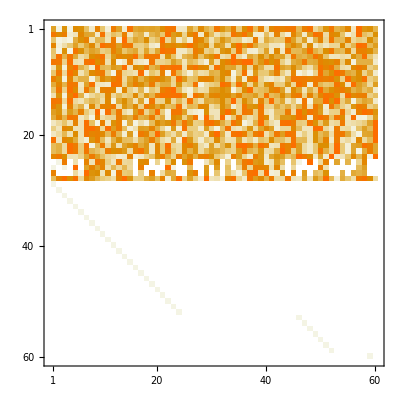

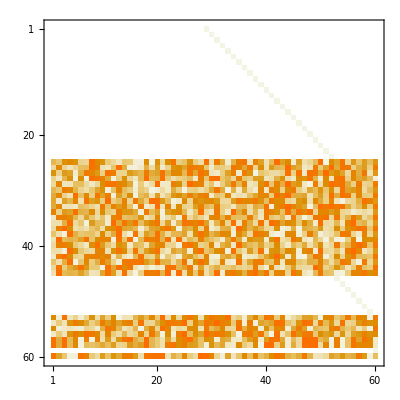

```mathematica
np1//ArrayReshape[#,{60,60}]&//MatrixPlot
np2//ArrayReshape[#,{60,60}]&//MatrixPlot
```

```mathematica
GroebnerBasis[syst // ReplaceAll[{m2->1,s->11,t->17}],variables,MonomialOrder->DegreeReverseLexicographic]; // AbsoluteTiming
```

{8.31275,Null}

```mathematica
gb=GroebnerBasis[syst // ReplaceAll[{m2->1,s->11,t->17}],variables,MonomialOrder->DegreeReverseLexicographic,Modulus->FFPrimeNo[0]]; // AbsoluteTiming
cmatsList=PolynomialReduce[Outer[Times,irreds,variables]//Flatten,gb,variables,MonomialOrder->DegreeReverseLexicographic,Modulus->FFPrimeNo[0]] // Map[Last]; // AbsoluteTiming
```

{5.69419,Null}

{37.0758,Null}

```mathematica
np1//ArrayReshape[#,{60,60}]&//Algebra`MatrixPowerMod[#,60,FFPrimeNo[0]]&; // AbsoluteTiming
np2//ArrayReshape[#,{60,60}]&//Algebra`MatrixPowerMod[#,60,FFPrimeNo[0]]&; // AbsoluteTiming
```

{0.018907,Null}

{0.0192,Null}

## Hexabox

```mathematica
baikMC = ;
vars={x10,x11,x12,x13}
```

{x10,x11,x12,x13}

```mathematica
ksub = {s12->1,s123->2,s23->3,s234->5,s34->7,s345->11,s45->13,s56->17};
ksub
```

{s12→1,s123→2,s23→3,s234→5,s34→7,s345→11,s45→13,s56→17}

```mathematica
system = {1-x0*baikMC}~Join~D[baikMC,{vars}]// ReplaceAll[ksub];
system // Variables//Sort
```

{s16,x0,x10,x11,x12,x13}

```mathematica
variables = vars~Join~{x0}
```

{x10,x11,x12,x13,x0}

```mathematica
irreds=FindIrreducibleMonomials[system,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{x10 x11,x11^2,x10 x12,x11 x12,x12^2,x10 x13,x11 x13,x12 x13,x13^2,x0 x10,x0 x11,x0 x12,x0 x13,x0^2,x10,x11,x12,x13,x0,1}

```mathematica
cmats = BuildCompanionMatrices[system,variables,10,irreds,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]; // AbsoluteTiming
cmats
```

creating system seeds...done: 0.00656s

generating and sorting monomials...done: 0.774063s

preparing to generate system of size 15115 x 13935...done: 0.267129s

generating system...done: 0.948812s

building FiniteFlow Graph...done: 0.004225s

loading system data into FiniteFlow Graph...done: 0.879377s

learning irreducible monomials...done: 1.02459s

final number of equations needed: 2728

{4.39601,Null}

{ffGraph$626465522068481,{s16,extraparam},{j[1,1,0,0,0],j[0,2,0,0,0],j[1,0,1,0,0],j[0,1,1,0,0],j[0,0,2,0,0],j[1,0,0,1,0],j[0,1,0,1,0],j[0,0,1,1,0],j[0,0,0,2,0],j[1,0,0,0,1],j[0,1,0,0,1],j[0,0,1,0,1],j[0,0,0,1,1],j[0,0,0,0,2],j[1,0,0,0,0],j[0,1,0,0,0],j[0,0,1,0,0],j[0,0,0,1,0],j[0,0,0,0,1],j[0,0,0,0,0]},{SPQR`Private`m[x10$19],SPQR`Private`m[x11$20],SPQR`Private`m[x12$21],SPQR`Private`m[x13$22],SPQR`Private`m[x0$23]},{x10,x11,x12,x13,x0}}

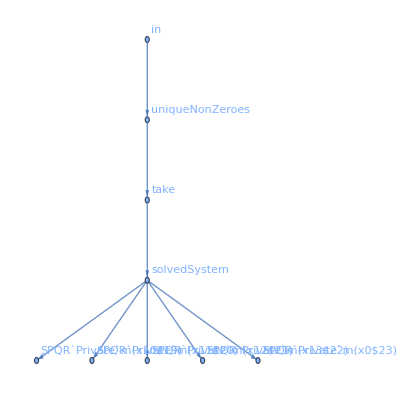

```mathematica
cmats // First // FFGraphDraw
```

```mathematica
FFGraphOutput[cmats//First,"solvedSystem"]
FFGraphEvaluate[cmats // First, {3,5}]; // AbsoluteTiming
```

{0.062519,Null}

```mathematica
(*override to check full graph*)
```

```mathematica
targ = BuildTargetCompanionMatrices[{x0},cmats]
```

{ffGraph$626465522068481,{s16,extraparam},{j[1,1,0,0,0],j[0,2,0,0,0],j[1,0,1,0,0],j[0,1,1,0,0],j[0,0,2,0,0],j[1,0,0,1,0],j[0,1,0,1,0],j[0,0,1,1,0],j[0,0,0,2,0],j[1,0,0,0,1],j[0,1,0,0,1],j[0,0,1,0,1],j[0,0,0,1,1],j[0,0,0,0,2],j[1,0,0,0,0],j[0,1,0,0,0],j[0,0,1,0,0],j[0,0,0,1,0],j[0,0,0,0,1],j[0,0,0,0,0]},{SPQR`Private`m[o$24]},{x10,x11,x12,x13,x0}}

```mathematica
np1=FFGraphEvaluate[targ // First, {3,5}]; // AbsoluteTiming
np1 // Length
np1 // First
```

{0.062286,Null}

400

4520409265322254767

```mathematica
chargraph=BuildCharacteristicPolynomial[targ,1]; // AbsoluteTiming
```

{0.020574,Null}

```mathematica
a=FFGraphEvaluate[chargraph // First, {3,5}]; // AbsoluteTiming
```

{0.063247,Null}

```mathematica
a//First
np1//ArrayReshape[#,{20,20}]&//Det[#,Modulus->FFPrimeNo[0]]&
```

4614604308199671571

4614604308199671571

```mathematica
a[[-2]]
-np1//ArrayReshape[#,{20,20}]&//Tr//Mod[#,FFPrimeNo[0]]&
```

929279158094131125

929279158094131125

```mathematica
np1//ArrayReshape[#,{20,20}]&//CharacteristicPolynomial[#,λ]&//CoefficientList[#,λ]&//Mod[#,FFPrimeNo[0]]&
%==a
```

{4614604308199671571,8053232881456436393,4777143244509390996,8213683400071331144,5522463232053696019,2870909861206988549,5926768213849753433,4169121472701841077,5355704372267779529,4867283041473823446,7256059087801831911,1196835615701634915,2607623170245497289,762631978927366274,3394738761231255534,3481267593239766064,73324726518776796,8336831622918700571,4736661520864840009,929279158094131125,1}

True

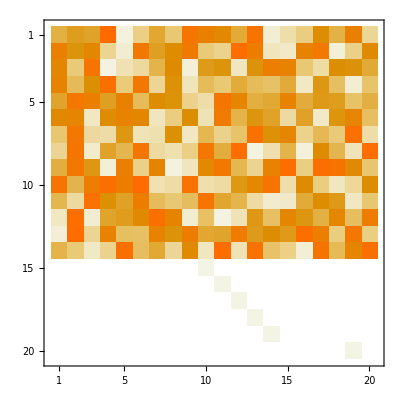

```mathematica
np1//ArrayReshape[#,{20,20}]&//MatrixPlot
```